```mathematica
hexToRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&;
colors=hexToRGB[#]&/@{"#f20060","#29339b","#c6d8ff","#7fff3a","#7692ff","#ff16e3"}
```

{RGBColor[0.9490196078431372, 0., 0.3764705882352941],RGBColor[0.16078431372549018, 0.2, 0.6078431372549019],RGBColor[0.7764705882352941, 0.8470588235294118, 1.],RGBColor[0.4980392156862745, 1., 0.22745098039215686],RGBColor[0.4627450980392157, 0.5725490196078431, 1.],RGBColor[1., 0.08627450980392157, 0.8901960784313725]}

## Resistance

```mathematica
SetDirectory[NotebookDirectory[]];
rawData=Import["./data/experimentsOutput.csv"];
data={#[[1]]//Round,#[[2]]//Round,#[[4]]//Round,#[[5]]//Round,#[[6]],#[[7]],#[[8]],#[[9]],#[[10]]}&/@rawData;
{d,r,s}={1,5,100};
labels={"R1","R2","R1 ∩ R2", "R1 ∪ R2", "SS"};
```

```mathematica
out=Table[
steady=Table[
probe=(Cases[data,{i,h_,r,s,ra_,rb_,un_,in_,ss_}->{h/100,ra,rb,un,in,ss}]//Sort);
{probe[[All,1]],probe[[All,j]]}//Transpose
,{i,1,6}];

hSamples=steady[[All,All,1]]//Flatten//DeleteDuplicates//Sort;
lp1=ListPlot[steady[[All,2;;All]]
,AspectRatio->1
,Frame->True
,FrameStyle->Thick
,FrameTicks->{
{{{0,"0.0"},{.2,"0.2"},{.4,"0.4"},{.6,"0.6"},{.8,"0.8"},{1,"1.0"}},None},
{{{0,"0.0"},{.2,"0.2"},{.4,"0.4"},{.6,"0.6"},{.8,"0.8"},{1,"1.0"}},None}
}
,FrameTicksStyle->Directive[60]
,GridLines->Automatic
,ImageSize->750
,Joined->True
,PlotLabel->Style[labels[[j-1]],100]
,PlotLegends->None(*{"CRISPR","CRISPRX","tGD","tGDX","tGD Cross","tGDX Cross"}*)
,PlotMarkers->None
,PlotRange->{{.25,1},{0,1}}
,PlotStyle->({Thickness[.015],Opacity[.8],#}&/@If[True,colors[[1;;6]],colors[[3;;6]]])
,Prolog->{Dashed,Thickness[.001],Opacity[.5],Line[{{#,0},{#,1500}}]&/@hSamples}
];
lp2=ListPlot[{#}&/@If[j<3,steady[[1;;2,1]],steady[[3;;All,1]]]
,AspectRatio->1
,Frame->True
,FrameStyle->Thick
,FrameTicksStyle->Directive[40]
,GridLines->Automatic
,ImageSize->750
,Joined->False
,PlotLabel->Style[labels[[j-1]],100]
,PlotLegends->None
,PlotMarkers->None
,PlotRange->All
,PlotStyle->({PointSize[.025],Opacity[.75],#}&/@If[j<3,colors[[1;;2]],colors[[3;;6]]])
,Prolog->{Dashed,Line[{{#,0},{#,1500}}]&/@hSamples}
];
lp=Show[lp1,lp2];
Export["./images/00R_"<>ToString[j]<>".pdf",lp,ImageSize->1000]
,{j,2,5}]
```

{./images/00R_2.pdf,./images/00R_3.pdf,./images/00R_4.pdf,./images/00R_5.pdf}

## Resistance 2

```mathematica
SetDirectory[NotebookDirectory[]];
rawData=Import["./data/experimentsOutput.csv"];
data={#[[1]]//Round,#[[2]]//Round,#[[4]]//Round,#[[5]]//Round,#[[6]],#[[7]],#[[8]],#[[9]],#[[10]]}&/@rawData;
{d,r,s}={1,5,100};
labels={"R1","R2","R1 ∩ R2", "R1 ∪ R2", "SS"};
```

```mathematica
Table[
steady=Table[
probe=(Cases[data,{i,h_,r,s,ra_,rb_,un_,in_,ss_}->{h/100,ra,rb,un,in,ss}]//Sort);
{probe[[All,1]],probe[[All,j]]}//Transpose
,{i,1,6}];

hSamples=steady[[All,All,1]]//Flatten//DeleteDuplicates//Sort;
lp1=ListPlot[If[j<2,steady[[1;;2,2;;All]],steady[[3;;All,2;;All]]]
,AspectRatio->1
,Frame->True
,FrameStyle->Thick
,FrameTicks->{
{{{0,"0.0"},{.2,"0.2"},{.4,"0.4"},{.6,"0.6"},{.8,"0.8"},{1,"1.0"}},None},
{{{0,"0.0"},{.2,"0.2"},{.4,"0.4"},{.6,"0.6"},{.8,"0.8"},{1,"1.0"}},None}
}
,FrameTicksStyle->Directive[60]
,GridLines->Automatic
,ImageSize->750
,Joined->True
,PlotLabel->Style[labels[[j-1]],100]
,PlotLegends->None(*{"CRISPR","CRISPRX","tGD","tGDX","tGD Cross","tGDX Cross"}*)
,PlotMarkers->None
,PlotRange->{{.25,1},{0,1}}
,PlotStyle->({Thickness[.015],Opacity[.8],#}&/@If[j<3,colors[[1;;2]],colors[[3;;6]]])
,Prolog->{Dashed,Thickness[.001],Opacity[.5],Line[{{#,0},{#,1500}}]&/@hSamples}
];
lp2=ListPlot[{#}&/@If[j<3,steady[[1;;2,1]],steady[[3;;All,1]]]
,AspectRatio->1
,Frame->True
,FrameStyle->Thick
,FrameTicksStyle->Directive[40]
,GridLines->Automatic
,ImageSize->750
,Joined->False
,PlotLabel->Style[labels[[j-1]],100]
,PlotLegends->None
,PlotMarkers->None
,PlotRange->All
,PlotStyle->({PointSize[.025],Opacity[.75],#}&/@If[j<3,colors[[1;;2]],colors[[3;;6]]])
,Prolog->{Dashed,Line[{{#,0},{#,1500}}]&/@hSamples}
];
lp=Show[lp1,lp2];
Export["./images/00R_"<>ToString[j]<>".pdf",lp,ImageSize->1000]
,{j,2,5}]
```

{./images/00R_2.pdf,./images/00R_3.pdf,./images/00R_4.pdf,./images/00R_5.pdf}

## Homing

```mathematica
SetDirectory[NotebookDirectory[]];
rawData=Import["./data/experimentsOutputH.csv"];
data={#[[1]]//Round,#[[2]]//Round,#[[4]]//Round,#[[5]]//Round,#[[6]],#[[7]],#[[8]],#[[9]],#[[10]]}&/@rawData;
{d,r,s}={1,5,100};
labels={"H","G","C ∩ G", "C ∪ G", "SS"};
```

```mathematica
indices = {1,2,3,4,5,6};
out=Table[
steady=Table[
probe=(Cases[data,{i,h_,r,s,ra_,rb_,un_,in_,ss_}->{h/100,ra,rb,un,in,ss}]//Sort);
{probe[[All,1]],probe[[All,j]]}//Transpose
,{i,indices}];

hSamples=steady[[All,All,1]]//Flatten//DeleteDuplicates//Sort;
lp1=ListPlot[If[j<3,steady[[1;;2,2;;All]],steady[[3;;All,2;;All]]]
,AspectRatio->1
,Frame->True
,FrameStyle->Thick
,FrameTicks->{
{{{0,"0.0"},{.2,"0.2"},{.4,"0.4"},{.6,"0.6"},{.8,"0.8"},{1,"1.0"}},None},
{{{0,"0.0"},{.2,"0.2"},{.4,"0.4"},{.6,"0.6"},{.8,"0.8"},{1,"1.0"}},None}
}
,FrameTicksStyle->Directive[60]
,GridLines->Automatic
,ImageSize->750
,Joined->True
,PlotLabel->Style[labels[[j-1]],100]
,PlotLegends->None(*{"CRISPR","CRISPRX","tGD","tGDX","tGD Cross","tGDX Cross"}*)
,PlotMarkers->None
,PlotRange->{{.5,1},{0,1}}
,PlotStyle->({Thickness[.015],Opacity[.8],#}&/@If[j<3,colors[[1;;2]],colors[[3;;6]]])
,Prolog->{Dashed,Thickness[.001],Opacity[.5],Line[{{#,0},{#,1500}}]&/@hSamples}
]
lp2=ListPlot[{#}&/@If[j<3,steady[[1;;2,1]],steady[[3;;All,1]]]
,AspectRatio->1
,Frame->True
,FrameStyle->Thick
,FrameTicksStyle->Directive[40]
,GridLines->Automatic
,ImageSize->750
,Joined->False
,PlotLabel->Style[labels[[j-1]],100]
,PlotLegends->None
,PlotMarkers->None
,PlotRange->All
,PlotStyle->({PointSize[.025],Opacity[.75],#}&/@If[j<3,colors[[1;;2]],colors[[3;;6]]])
,Prolog->{Dashed,Line[{{#,0},{#,1500}}]&/@hSamples}
](*;
lp=Show[lp1,lp2];
Export["./images/00H_"<>ToString[j]<>".pdf",lp,ImageSize->1000]*)
,{j,2,5}];
```

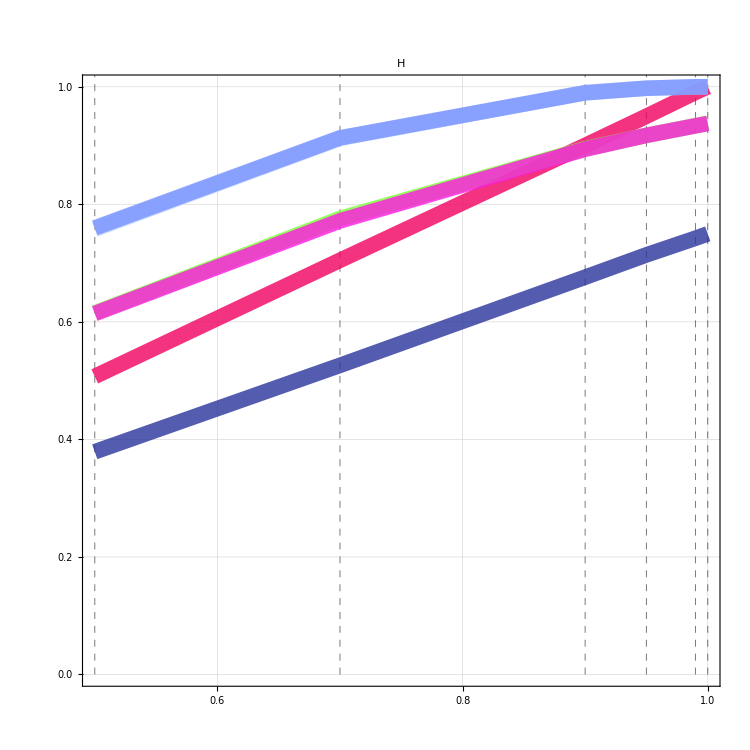

./images/00H.pdf

```mathematica
exp=Show[out[[1]],out[[4]]]
Export["./images/00H.pdf",exp,ImageSize->1000]
```

## Homing 2

```mathematica
ix={1,2,5};
out=Table[
steady=Table[
probe=(Cases[data,{i,h_,r,s,ra_,rb_,un_,in_,ss_}->{h/100,ra,rb,un,in,ss}]//Sort);
{probe[[All,1]],probe[[All,j]]}//Transpose
,{i,ix}];
labels={"H","G","C ∩ G", "C ∪ G", "SS"};

hSamples=steady[[All,All,1]]//Flatten//DeleteDuplicates//Sort;
lp1=ListPlot[If[j<2,steady[[1;;2,2;;All]],steady[[3;;All,2;;All]]]
,AspectRatio->1
,Frame->True
,FrameStyle->Thick
,FrameTicks->{
{{{0,"0.0"},{.2,"0.2"},{.4,"0.4"},{.6,"0.6"},{.8,"0.8"},{1,"1.0"}},None},
{{{0,"0.0"},{.2,"0.2"},{.4,"0.4"},{.6,"0.6"},{.8,"0.8"},{1,"1.0"}},None}
}
,FrameTicksStyle->Directive[60]
,GridLines->Automatic
,ImageSize->750
,Joined->True
,PlotLabel->Style[labels[[j-1]],100]
,PlotLegends->None(*{"CRISPR","CRISPRX","tGD","tGDX","tGD Cross","tGDX Cross"}*)
,PlotMarkers->None
,PlotRange->{{.5,1},{0,1}}
,PlotStyle->({Thickness[.015],Opacity[.8],#}&/@If[j<3,colors[[1;;2]],colors[[5;;6]]])
,Prolog->{Dashed,Thickness[.001],Opacity[.5],Line[{{#,0},{#,1500}}]&/@hSamples}
](*;
lp2=ListPlot[{#}&/@If[j<3,steady[[1;;2,1]],steady[[3;;All,1]]]
,AspectRatio->1
,Frame->True
,FrameStyle->Thick
,FrameTicksStyle->Directive[40]
,GridLines->Automatic
,ImageSize->750
,Joined->False
,PlotLabel->Style[labels[[j-1]],100]
,PlotLegends->None
,PlotMarkers->None
,PlotRange->All
,PlotStyle->({PointSize[.025],Opacity[.75],#}&/@If[j<3,colors[[1;;2]],colors[[3;;6]]])
,Prolog->{Dashed,Line[{{#,0},{#,1500}}]&/@hSamples}
];
lp=Show[lp1,lp2];
Export["./images/01H_"<>ToString[j]<>".pdf",lp,ImageSize->1000]*)
,{j,2,5}];
```

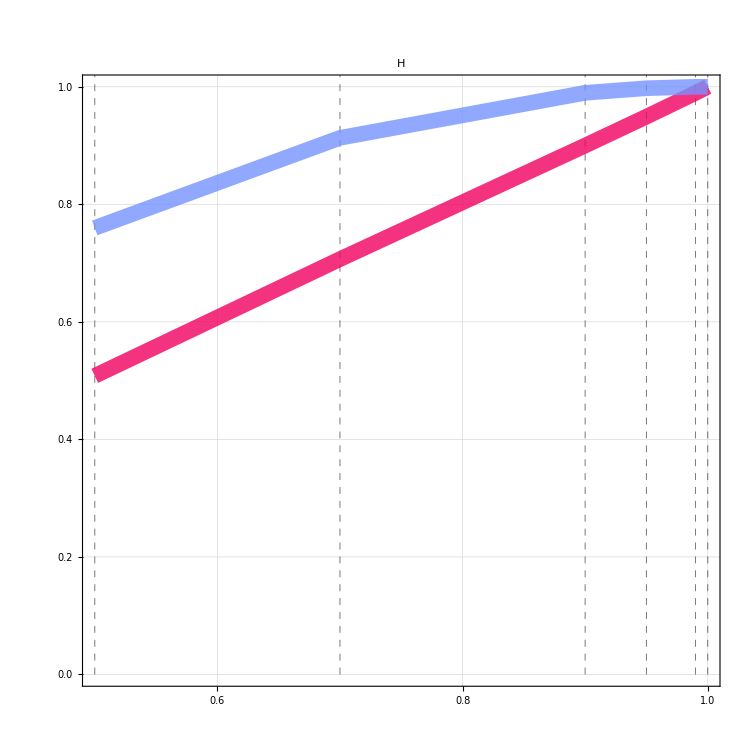

./images/00Hb.pdf

```mathematica
exp=Show[out[[1]],out[[4]]]
Export["./images/00Hb.pdf",exp,ImageSize->1000]
```

## Steady State

```mathematica
Table[
steady=Table[
probe=(Cases[data,{i,h_,r,s,ra_,rb_,un_,in_,ss_}->{h/100,ra,rb,un,in,ss}]//Sort);
{probe[[All,1]],probe[[All,j]]}//Transpose
,{i,1,6}];

hSamples=steady[[All,All,1]]//Flatten//DeleteDuplicates//Sort;
lp1=ListPlot[steady[[All,2;;All]]
,AspectRatio->1
,Frame->True
,FrameStyle->Thick
,FrameTicksStyle->Directive[40]
,GridLines->Automatic
,ImageSize->750
,Joined->True
,PlotLabel->Style[labels[[j-1]],100]
,PlotLegends->{"CRISPR","CRISPRX","tGD","tGDX","tGD Cross","tGDX Cross"}
,PlotMarkers->None
,PlotRange->{{.5,1},{0,All}}
,PlotStyle->({Thickness[.015],Opacity[.8],#}&/@colors)
,Prolog->{Dashed,Thickness[.0025],Opacity[.5],Line[{{#,0},{#,1500}}]&/@hSamples}
];
lp2=ListPlot[{#}&/@steady[[All,1]]
,AspectRatio->1
,Frame->True
,FrameStyle->Thick
,FrameTicksStyle->Directive[40]
,GridLines->Automatic
,ImageSize->750
,Joined->False
,PlotLabel->Style[labels[[j-1]],100]
,PlotLegends->None
,PlotMarkers->None
,PlotRange->All
,PlotStyle->({PointSize[.025],Opacity[.75],#}&/@colors)
,Prolog->{Dashed,Line[{{#,0},{#,1500}}]&/@hSamples}
];
lp=Show[lp1,lp2];
Export["./images/01SS_"<>ToString[j]<>".pdf",lp]
,{j,6,6}]
```

{./images/01SS_6.pdf}

```mathematica
ix={1,5};
Table[
steady=Table[
probe=(Cases[data,{i,h_,r,s,ra_,rb_,un_,in_,ss_}->{h/100,ra,rb,un,in,ss}]//Sort);
{probe[[All,1]],probe[[All,j]]}//Transpose
,{i,ix}];

hSamples=steady[[All,All,1]]//Flatten//DeleteDuplicates//Sort;
lp1=ListPlot[steady[[All,2;;All]]
,AspectRatio->1
,Frame->True
,FrameStyle->Thick
,FrameTicksStyle->Directive[40]
,GridLines->Automatic
,ImageSize->750
,Joined->True
,PlotLabel->Style[labels[[j-1]],100]
,PlotLegends->({"CRISPR","CRISPRX","tGD","tGDX","tGD Cross","tGDX Cross"}[[#]]&/@ix)
,PlotMarkers->None
,PlotRange->{{.5,1},{0,All}}
,PlotStyle->({Thickness[.015],Opacity[.8],#}&/@(colors[[#]]&/@ix))
,Prolog->{Dashed,Thickness[.0025],Opacity[.5],Line[{{#,0},{#,1500}}]&/@hSamples}
];
lp2=ListPlot[{#}&/@steady[[All,1]]
,AspectRatio->1
,Frame->True
,FrameStyle->Thick
,FrameTicksStyle->Directive[40]
,GridLines->Automatic
,ImageSize->750
,Joined->False
,PlotLabel->Style[labels[[j-1]],100]
,PlotLegends->None
,PlotMarkers->None
,PlotRange->All
,PlotStyle->({PointSize[.025],Opacity[.75],#}&/@(colors[[#]]&/@ix))
,Prolog->{Dashed,Line[{{#,0},{#,1500}}]&/@hSamples}
];
lp=Show[lp1,lp2];
Export["./images/01SS_"<>ToString[j]<>".pdf",lp]
,{j,6,6}]
```

{./images/01SS_6.pdf}

## Legend

```mathematica
SwatchLegend[colors,{"CRISPR","CRISPRX","tGD","tGDX","tGD Cross","tGDX Cross"},LegendMarkerSize->50,LabelStyle->50]
Export["legend.pdf",%]
```

legend.pdf